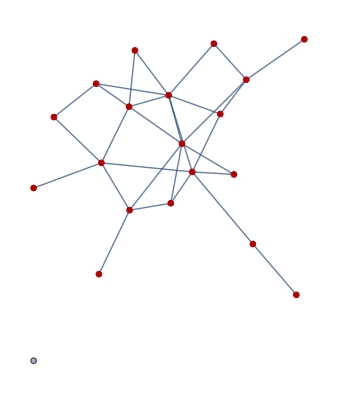

```mathematica
DFS[graph_,startnode_]:=Module[
{v,vl,links,l,bag,pos,visited,Dfs,visitedpos},
(*--------Global variables--------*)
v=VertexList[graph];
links=EdgeList[graph];
vl=Length[v];
l=Length[links];
bag={};
visited=ConstantArray[False,vl];
pos[list_,element_]:=Flatten[Position[list,element]][[1]];
(*----------Dfs procedure---------*)

Dfs[at_]:=Module[
{neighborhood,neighbours,ln,p,visitedposdfs},
neighborhood={VertexList@#,#}&@IncidenceList[graph,at];
neighbours=neighborhood[[1]];
ln=Length[neighbours];
p=pos[v,at];
If[visited[[p]]==True,Return;,
If[ln>0,
visited[[p]]=True;
bag=Append[bag,v[[p]]],
Return;
]
];

For[j=1,j<Length[neighbours]+1,j++,
visitedposdfs=pos[v,neighbours[[j]]];
If[visited[[visitedposdfs]]==False,
Dfs[neighbours[[j]]],Continue[]
];
];
];

(*--------Dfs for all nodes-------*)
Dfs[startnode];
For[i=1,i<vl+1,i++,
visitedpos=pos[v,v[[i]]];
If[visited[[visitedpos]]==False,
Dfs[v[[i]]],
Continue[]
]
];
bag
];
g=RandomGraph[{20,30}];
dfs=DFS[g,4];
HighlightGraph[g,dfs]
```

{1,13}

{1,13,17,18}

{11,17,13}

{11,12,17}

{11,12,20}

{12,20}

{2,5}

{2,5}

{3,16}

{3,16}

{}

{}

{}

«2 more identical outputs»

{10,15}

{10,15}

{14,19}

{14,19}

{13,18}

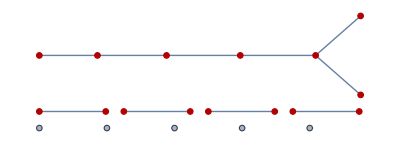

```mathematica
g=RandomGraph[{20,10}];
dfs=DFS[g,1];
HighlightGraph[g,dfs]
```